## Configuration

```mathematica
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

Notebook load complete.

```mathematica
timeLimit=0.5;(* in minutes *)(* set this higher overnight *)
timeLimit=timeLimit*60;
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

```mathematica
$Assumptions=0<eps<1/10 && 0<M<Q && 0<p1m<Q&&0<p1p<Q&&0<p2m<Q&&0<p2p<Q&&0<qm<Q&&0<qp<Q&&km∈Reals&&0≤ x≤ 1&&0≤ y≤ 1&&0≤ z≤ 1&&0≤ w≤ 1/3&&p3p∈Reals&&p3m∈Reals&&p4p∈Reals&&p4m∈Reals&&lambda∈Reals&&Q>0&&1/3>tau>0&&muMS>0&&1/3>tau>0&&0<qhatp<1&&0<qhatm<1&&xi>0&&nu>0&&muPrime>0&&nuPrime>0&&mu1>0;

waveZ=(alphabar/2)(1/eps-LM-1/2)

ansQCD=-2 zeta2 ᾱ+(ᾱ)/(2 ϵ)-2 ᾱ-1/2 Lis^2 ᾱ+(3 Lis ᾱ)/2+Lis LM ᾱ-(LM^2 ᾱ)/2-2 LM ᾱ-waveZ/.Lis->LQ//Expand
```

1/2 ᾱ (-LM+1/ϵ-1/2)

-2 ζ_2 ᾱ-(7 ᾱ)/4-1/2 LM^2 ᾱ-(3 LM ᾱ)/2+LM LQ ᾱ-(LQ^2 ᾱ)/2+(3 LQ ᾱ)/2

```mathematica
ansQCD/.LQ->L+LM/.Pi^2->6zeta2//Expand
%*2//Expand
(%//Expand)/.Pi^2->6zeta2
```

-2 ζ_2 ᾱ-(7 ᾱ)/4-1/2 L^2 ᾱ+(3 L ᾱ)/2

-4 ζ_2 ᾱ-(7 ᾱ)/2+L^2 (-ᾱ)+3 L ᾱ

-4 ζ_2 ᾱ-(7 ᾱ)/2+L^2 (-ᾱ)+3 L ᾱ

## Spacelike

### Canonical Way

```mathematica
(x)^-eps/(1-x)/.x->x/(1-I*zerop)
tempAns=Integrate[%,{x,0,Infinity},Assumptions->eps>0&&zerop>0]
```

((x/(1-ⅈ 0^+))^-ϵ)/(1-x/(1-ⅈ 0^+))

-π (1-ⅈ 0^+)^(ϵ+1) (-1+ⅈ 0^+)^-ϵ csc(π ϵ)

```mathematica
(* add the minus sign back in becasue mathematica is stupid *)
-tempAns//FullSimplify
Series[%,{eps,0,1}]//Normal
tempAnsSeries=%+1/(1-eps)/.Log[-1-I*zerop]->-I*Pi/.Log[-1+I*Pi]->I*Pi/.zerop->0

(* see above we have to explicitly add 1/(1-eps) ? that comes from  the QCD integral of the kp term in the numerator that my code can't do *)
```

π (1-ⅈ 0^+)^(ϵ+1) (-1+ⅈ 0^+)^-ϵ csc(π ϵ)

(1-ⅈ 0^+)/ϵ+π ϵ (1/6 π (1-ⅈ 0^+)+((1-ⅈ 0^+) log^2(1-ⅈ 0^+))/(2 π)+((1-ⅈ 0^+) log^2(-1+ⅈ 0^+))/(2 π)-((1-ⅈ 0^+) log(-1+ⅈ 0^+) log(1-ⅈ 0^+))/π)+π (((1-ⅈ 0^+) log(1-ⅈ 0^+))/π-((1-ⅈ 0^+) log(-1+ⅈ 0^+))/π)

-(π^2 ϵ)/3+1/(1-ϵ)+1/ϵ-ⅈ π

```mathematica
Pi*(-1+I*zerop)^(-eps)*Csc[Pi*eps]//FullSimplify
Series[%,{eps,0,1}]//Normal
%/.Log[-1-I*zerop]->-I*Pi/.Log[-1+I*Pi]->I*Pi/.zerop->0
```

π (-1+ⅈ 0^+)^-ϵ csc(π ϵ)

1/6 ϵ (π^2+3 log^2(-1+ⅈ 0^+))-log(-1+ⅈ 0^+)+1/ϵ

-(π^2 ϵ)/3+1/ϵ-ⅈ π

```mathematica
(* the following from Simon and Ray's paper, eqs. 30-32 *)
igrandN=-(1-km/p1m)^(1-eps)/km
igrandNbar=(p2p/M^2)*(1-(km*p2p/M^2)^-eps)/(1-p2p*km/M^2)//Expand
igrandOver=-1/km

(* do the well-defined integral -- the one with (kp*p2p)^-eps in the numerator -- by hand. See above *)
igrandNbarDivPart=igrandNbar/.(km*p2p/M^2)^(-eps)->0
```

-((1-k^-/p_1^-)^(1-ϵ))/k^-

p_2^+/(M^2 (1-(k^- p_2^+)/M^2))-(p_2^+ ((k^- p_2^+)/M^2)^-ϵ)/(M^2 (1-(k^- p_2^+)/M^2))

-1/k^-

p_2^+/(M^2 (1-(k^- p_2^+)/M^2))

```mathematica
(* from 0 to p1m *)
igrandN-igrandOver/.DiracDelta[_]->0/.M->Sqrt[M^2-I*zerop]
intLowerNover=Integrate[%,{km,0,p1m},Assumptions->0<zerop<M^2<p1m*p2p]
intLowerSeriesNover=Series[intLowerNover,{eps,0,1},Assumptions->M^2<p1m*p2p]//Normal

(* from 0 to p1m *)
igrandNbarDivPart/.DiracDelta[_]->0/.M->Sqrt[M^2-I*zero]/.p2p->A/.km->x
intLowerNbar=Integrate[%,{x,0,B},Assumptions->zero>0]/.A->p2p/.B->p1m
intLowerSeriesNbar=Series[intLowerNbar,{eps,0,1},Assumptions->M^2<p1m*p2p]//Normal


intLowerSeries=(intLowerSeriesNover+intLowerSeriesNbar/. 1+A_/B_:>(B+A)/(B)/. 1-A_/B_:>(B-A)/(B)//expLogs)/.Log[M^2-p2p*p1m-I*zero]->Log[p2p*p1m-M^2]-I*Pi/.Log[M^2-p2p*p1m+I*zero]->Log[p2p*p1m-M^2]+I*Pi/.Log[M^2-I*zero]->Log[M^2]
```

1/k^--((1-k^-/p_1^-)^(1-ϵ))/k^-

1-ϵ

(1-π^2/6) ϵ+1

A/((M^2-ⅈ zero) (1-(A x)/(M^2-ⅈ zero)))

-log(1-(p_2^+ p_1^-)/(M^2-ⅈ zero))

-log(1-(p_2^+ p_1^-)/(M^2-ⅈ zero))

-log(p_2^+ p_1^--M^2)+log(M^2)+(1-π^2/6) ϵ+ⅈ π+1

```mathematica
(* from p1m to infinity *)
igrandNbarDivPart-igrandOver/.DiracDelta[_]->0/.M->Sqrt[M^2-I*zerop]
intUpper=Integrate[%,{km,p1m,Infinity},Assumptions->0<zerop<M^2<p1m*p2p]/.Log[1-(M^2-I*zerop)/(p2p*p1m)]->Log[(p2p*p1m-M^2)/(p1m*p2p)]
```

1/k^-+p_2^+/((M^2-ⅈ 0^+) (1-(k^- p_2^+)/(M^2-ⅈ 0^+)))

log((p_2^+ p_1^--M^2)/(p_2^+ p_1^-))

```mathematica
Integrate[1/(x+I*zerop),{x,0,z}]
```

log(1-(ⅈ z)/0^+)

```mathematica
prefac=alphabar(muMS^2Exp[EulerGamma]/(M^2))^(eps)Gamma[eps]
igrandTotal=prefac*(   tempAnsSeries+intLowerSeries+intUpper   )

igrandTotal2=Series[%,{eps,0,0}]//Normal

igrandTotal2
Simplify[%,Assumptions->M>0&&p1m>0&&p2p>0&&muMS>0]//expLogs//Expand
ansUsual=%-waveZ/.Log[M]->LM/2+Log[muMS]/.Log[p1m]->Log[p1m*p2p]-Log[p2p]/.Log[p1m*p2p]->LQ+2Log[muMS]//Expand


SeriesCoefficient[ansQCD-ansUsual,{eps,0,0}]//Expand
Series[(1+ansQCD)/(1+ansUsual),{alphabar,0,1}]//Normal//Expand
c2Usual=(%-1)/alphabar//Expand
```

ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ

ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ (-log(p_2^+ p_1^--M^2)+log((p_2^+ p_1^--M^2)/(p_2^+ p_1^-))+log(M^2)+(1-π^2/6) ϵ-(π^2 ϵ)/3+1/(1-ϵ)+1/ϵ+1)

(ᾱ)/ϵ^2+(ᾱ (log(μ_OverBar[MS]^2/M^2)-log(p_2^+ p_1^--M^2)+log((p_2^+ p_1^--M^2)/(p_2^+ p_1^-))+log(M^2)+2))/ϵ-1/12 ᾱ (12 log(p_2^+ p_1^--M^2) log(μ_OverBar[MS]^2/M^2)-12 log((p_2^+ p_1^--M^2)/(p_2^+ p_1^-)) log(μ_OverBar[MS]^2/M^2)-6 log^2(μ_OverBar[MS]^2/M^2)-12 log(M^2) log(μ_OverBar[MS]^2/M^2)-24 log(μ_OverBar[MS]^2/M^2)+5 π^2-24)

(ᾱ)/ϵ^2+(ᾱ (log(μ_OverBar[MS]^2/M^2)-log(p_2^+ p_1^--M^2)+log((p_2^+ p_1^--M^2)/(p_2^+ p_1^-))+log(M^2)+2))/ϵ-1/12 ᾱ (12 log(p_2^+ p_1^--M^2) log(μ_OverBar[MS]^2/M^2)-12 log((p_2^+ p_1^--M^2)/(p_2^+ p_1^-)) log(μ_OverBar[MS]^2/M^2)-6 log^2(μ_OverBar[MS]^2/M^2)-12 log(M^2) log(μ_OverBar[MS]^2/M^2)-24 log(μ_OverBar[MS]^2/M^2)+5 π^2-24)

(ᾱ)/ϵ^2+(2 ᾱ)/ϵ-(5 π^2 ᾱ)/12+2 ᾱ-2 ᾱ log^2(M)-4 ᾱ log(M)+2 ᾱ log(M) log(p_2^+)+2 ᾱ log(M) log(p_1^-)-2 ᾱ log(p_2^+) log(μ_OverBar[MS])-2 ᾱ log(p_1^-) log(μ_OverBar[MS])+(2 ᾱ log(μ_OverBar[MS]))/ϵ+2 ᾱ log^2(μ_OverBar[MS])+4 ᾱ log(μ_OverBar[MS])-(ᾱ log(p_2^+))/ϵ-(ᾱ log(p_1^-))/ϵ

(ᾱ)/ϵ^2+(3 ᾱ)/(2 ϵ)-(5 π^2 ᾱ)/12+(9 ᾱ)/4-1/2 LM^2 ᾱ-(3 LM ᾱ)/2+LM LQ ᾱ-(LQ ᾱ)/ϵ

-2 ζ_2 ᾱ+(5 π^2 ᾱ)/12-4 ᾱ-1/2 LQ^2 ᾱ+(3 LQ ᾱ)/2

-2 ζ_2 ᾱ-(ᾱ)/ϵ^2-(3 ᾱ)/(2 ϵ)+(5 π^2 ᾱ)/12-4 ᾱ-1/2 LQ^2 ᾱ+(LQ ᾱ)/ϵ+(3 LQ ᾱ)/2+1

-2 ζ_2-LQ^2/2+LQ/ϵ+(3 LQ)/2-1/ϵ^2-3/(2 ϵ)+(5 π^2)/12-4

```mathematica
ansUsual*2//Expand
c2Usual//Expand
```

(2 ᾱ)/ϵ^2+(3 ᾱ)/ϵ-(5 π^2 ᾱ)/6+(9 ᾱ)/2+LM^2 (-ᾱ)-3 LM ᾱ+2 LM LQ ᾱ-(2 LQ ᾱ)/ϵ

-2 ζ_2-LQ^2/2+LQ/ϵ+(3 LQ)/2-1/ϵ^2-3/(2 ϵ)+(5 π^2)/12-4

### Plotting Overlap Influence

-(1-z)^(9/10)/z

100/(1-100 z)

-1/z

1/z+100/(1-100 z)

1/z-(1-z)^(9/10)/z

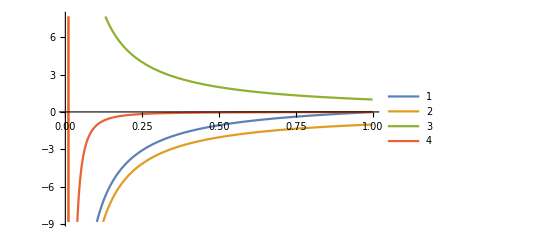

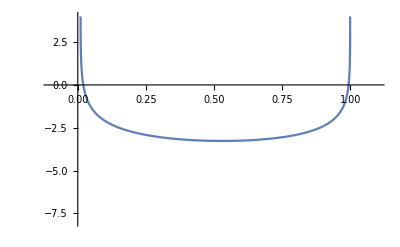

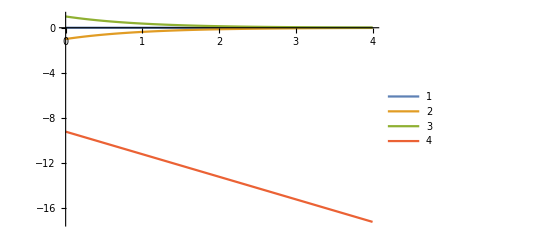

```mathematica
(* influence of overlap for nu=Q *)

plotMeLowerN=igrandN*measureChangeN/.km->z*p1m/.measureChangeN->p1m/.eps->10^-1
plotMeLowerNbar=igrandNbarDivPart*measureChangeNbar/.km->nu^2*z/p2p/.measureChangeNbar->nu^2/p2p/.DiracDelta[_]->0/.nu->10M/.eps->10^-1//Simplify
plotMeLowerOverlap=igrandOver*measureChangeOver/.km->z*nu1/.measureChangeOver->nu1
plotMeLowerDiff=plotMeLowerNbar-plotMeLowerOverlap (* this is "how much of the nbar sector we're allowing to populate our result" *)
plotMeOtherLowerDiff=plotMeLowerN-plotMeLowerOverlap

Plot[{plotMeLowerN,plotMeLowerNbar,-plotMeLowerOverlap,plotMeLowerDiff},{z,1/1000,1},PlotLegends->Automatic]
(* see how the overlap only allows very small values of km to contribute, and as km approaches zero it regulates the n-sector divergence *)

importanceLowerQ=plotMeLowerDiff/plotMeLowerN;
Plot[Log@importanceLowerQ,{z,0,1},PlotRange->{{-0.1,1.1},{-8,4}}]

plotMeUpperN=0/.eps->10^-5;
plotMeUpper=igrandNbarDivPart*measureChangeNbar/.km->nu^2*z/p2p/.measureChangeNbar->nu^2/p2p/.DiracDelta[_]->0/.nu->100M/.eps->10^-15/.z->Exp[xii]//Simplify;
plotMeUpperOverlap=igrandOver*measureChangeOver/.km->z*nu1/.measureChangeOver->nu1/.z->Exp[xii];
plotMeUpperDiff=plotMeUpper-plotMeUpperOverlap;

Plot[{plotMeUpperN,plotMeUpper,-plotMeUpperOverlap,Log@-plotMeUpperDiff},{xii,0,4},PlotLegends->Automatic]
```

-(1-z)^(999999999999999/1000000000000000)/z

1/(1-z)

-1/z

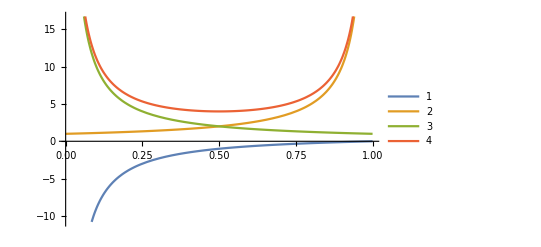

-Graphics-

1/(1-ⅇ^xii)

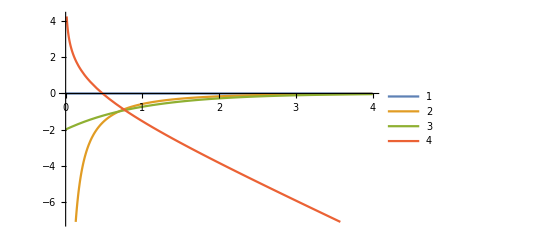

```mathematica
(* influence of overlap for nu=Q *)

plotMeLowerN=igrandN*measureChangeN/.km->z*p1m/.measureChangeN->p1m/.eps->10^-15
plotMeLowerNbar=igrandNbarDivPart*measureChangeNbar/.km->nu^2*z/p2p/.measureChangeNbar->nu^2/p2p/.DiracDelta[_]->0/.nu->M/.eps->10^-15//Simplify
plotMeLowerOverlap=igrandOver*measureChangeOver/.km->z*nu1/.measureChangeOver->nu1
plotMeLowerDiff=plotMeLowerNbar-plotMeLowerOverlap; (* this is "how much of the nbar sector we're allowing to populate our result" *)
plotMeOtherLowerDiff=plotMeLowerN-plotMeLowerOverlap;

Plot[{plotMeLowerN,plotMeLowerNbar,-plotMeLowerOverlap,plotMeLowerDiff},{z,0,1},PlotLegends->Automatic]

importanceLowerQ=plotMeLowerDiff/plotMeLowerN;
Plot[Log@importanceLowerQ,{z,0,1},PlotRange->{{-0.1,1.1},{-8,4}}]

plotMeUpperN=0/.eps->10^-5;
plotMeUpper=igrandNbarDivPart*measureChangeNbar/.km->nu^2*z/p2p/.measureChangeNbar->nu^2/p2p/.DiracDelta[_]->0/.nu->M/.eps->10^-15/.z->Exp[xii]//Simplify
plotMeUpperOverlap=igrandOver*measureChangeOver/.km->z*nu1/.measureChangeOver->nu1/.z->Exp[xii];
plotMeUpperDiff=plotMeUpper-plotMeUpperOverlap;

Plot[{plotMeUpperN,plotMeUpper,2plotMeUpperOverlap,Log@-plotMeUpperDiff},{xii,0,4},PlotLegends->Automatic]
```

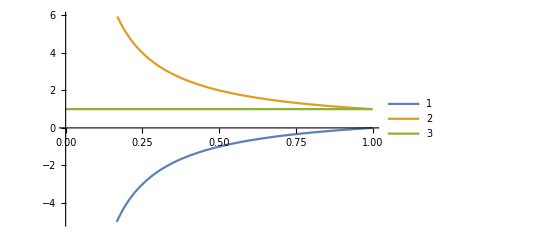

```mathematica
Plot[{plotMeLowerN,-plotMeLowerOverlap,plotMeOtherLowerDiff},{z,0,1},PlotLegends->Automatic]
```

## Exponent-Type Regulator

```mathematica
(*ansN=-alphabar*(muMS^2*Exp[EulerGamma]/M^2)^eps(nu1/p1m)^eta1 Gamma[eps]Gamma[2-eps]Gamma[-eta1]/(Gamma[1]Gamma[2-eps-eta1])
ansNb=ansN/.nu1->nu2/.eta1->eta2/.p1m->p2p

total0=ansN+ansNb/.eta1->eta/.eta2->eta/.nu1->nu/.nu2->nu
totSer0=Series[total0,{eps,0,0}]//Normal
ZEps=SeriesCoefficient[totSer0,{eps,0,-1}]
totSer1=Series[totSer0-ZEps/eps,{eta,0,0}]//Normal
ZEta=SeriesCoefficient[totSer1,{eta,0,-1}]
totalFinite=totSer1-ZEta/eta/.Pi^2->6zeta2//expLogs//Expand//FullSimplify

Ztot=ZEta/eta+ZEps/eps*)
```

```mathematica
ansN=-alphabar*(muMS^2*Exp[EulerGamma]/M^2)^eps(nu1/p1m)^eta1 Gamma[eps]Gamma[2-eps]Gamma[-eta1]/(Gamma[1]Gamma[2-eps-eta1])
ansNb=ansN/.nu1->nu2/.eta1->eta2/.p1m->p2p

matElemTot=ansN+ansNb-waveZ/.eta1->eta/.eta2->eta/.nu1->nu/.nu2->nu
totSer0=Series[matElemTot,{eta,0,0}]//Normal
ZEta=SeriesCoefficient[totSer0,{eta,0,-1}]
totSer1=Series[totSer0-ZEta/eta,{eps,0,0}]//Normal
ZEps=SeriesCoefficient[totSer1,{eps,0,-1}]
totalFinite=totSer1-ZEps/eps/.Pi^2->6zeta2//expLogs//Expand//FullSimplify

Ztot=ZEta/eta+ZEps/eps
```

-(ⅇ^(ℽ ϵ) ᾱ -η_1 2-ϵ ϵ (ν_1/p_1^-)^η_1 (μ_OverBar[MS]^2/M^2)^ϵ)/(-η_1-ϵ+2)

-(ⅇ^(ℽ ϵ) ᾱ -η_2 2-ϵ ϵ (ν_2/p_2^+)^η_2 (μ_OverBar[MS]^2/M^2)^ϵ)/(-η_2-ϵ+2)

-1/2 ᾱ (-LM+1/ϵ-1/2)-(ⅇ^(ℽ ϵ) ᾱ -η 2-ϵ ϵ (ν/p_2^+)^η (μ_OverBar[MS]^2/M^2)^ϵ)/(-ϵ-η+2)-(ⅇ^(ℽ ϵ) ᾱ -η 2-ϵ ϵ (ν/p_1^-)^η (μ_OverBar[MS]^2/M^2)^ϵ)/(-ϵ-η+2)

-1/2 ᾱ (-LM+1/ϵ-1/2)+ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ (log(ν/p_2^+)+02-ϵ+ℽ)+ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ (log(ν/p_1^-)+02-ϵ+ℽ)+(2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η

2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ

-(π^2 ᾱ)/3+(9 ᾱ)/4+(LM ᾱ)/2+ᾱ log(ν/p_2^+) log(μ_OverBar[MS]^2/M^2)+ᾱ log(ν/p_1^-) log(μ_OverBar[MS]^2/M^2)+2 ᾱ log(μ_OverBar[MS]^2/M^2)+((3 ᾱ)/2+ᾱ log(ν/p_2^+)+ᾱ log(ν/p_1^-))/ϵ

(3 ᾱ)/2+ᾱ log(ν/p_2^+)+ᾱ log(ν/p_1^-)

1/4 ᾱ (-8 ζ_2+2 LM+8 log(p_2^+ p_1^-) log(M/μ_OverBar[MS])+16 (log(ν)+1) log(μ_OverBar[MS]/M)+9)

(2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η+((3 ᾱ)/2+ᾱ log(ν/p_2^+)+ᾱ log(ν/p_1^-))/ϵ

```mathematica
ansQCD-ansUsual
ansQCD-totalFinite
%/.LM->Log[M^2/muMS^2]/.LQ->Log[Q^2/muMS^2]/.Log[p1m*p2p]->2Log[Q]//expLogs//Expand
%//FullSimplify
Collect2[%,Log[Q]]
%/.Log[M]->LM/2+Log[muMS]//FullSimplify
%/.Log[Q]->LQ/2+Log[muMS]//FullSimplify
%/.Log[muMS/nu]->-LNUMU/2//FullSimplify
%/.LM^2-2LM*LNUMU->(LM-LNUMU)^2-LNUMU^2
%/.LM-LNUMU->LMNU
```

-2 ζ_2 ᾱ-(ᾱ)/ϵ^2-(3 ᾱ)/(2 ϵ)+(5 π^2 ᾱ)/12-4 ᾱ-1/2 LQ^2 ᾱ+(LQ ᾱ)/ϵ+(3 LQ ᾱ)/2

-2 ζ_2 ᾱ-(7 ᾱ)/4-1/2 LM^2 ᾱ-(3 LM ᾱ)/2+LM LQ ᾱ-1/4 ᾱ (-8 ζ_2+2 LM+8 log(p_2^+ p_1^-) log(M/μ_OverBar[MS])+16 (log(ν)+1) log(μ_OverBar[MS]/M)+9)-(LQ^2 ᾱ)/2+(3 LQ ᾱ)/2

-4 ᾱ+4 ᾱ log(ν) log(M)-2 ᾱ log^2(M)+4 ᾱ log(Q) log(μ_OverBar[MS])-4 ᾱ log(ν) log(μ_OverBar[MS])-3 ᾱ log(μ_OverBar[MS])-2 ᾱ log^2(Q)+3 ᾱ log(Q)

ᾱ (-(-4 log(ν) log(M)+2 log^2(M)+log(μ_OverBar[MS]) (4 log(ν)-4 log(Q)+3)+log(Q) (2 log(Q)-3)+4))

-ᾱ (-4 log(ν) log(M)+2 log^2(M)+4 log(ν) log(μ_OverBar[MS])+3 log(μ_OverBar[MS])+4)+ᾱ log(Q) (4 log(μ_OverBar[MS])+3)-2 ᾱ log^2(Q)

-1/2 ᾱ (LM^2-4 LM log(ν)+(4 LM-8 log(Q)+6) log(μ_OverBar[MS])+4 log^2(μ_OverBar[MS])+4 log^2(Q)-6 log(Q)+8)

-1/2 ᾱ (LM^2+4 LM log(μ_OverBar[MS]/ν)+(LQ-3) LQ+8)

-1/2 ᾱ (LM^2-2 LM LNUMU+(LQ-3) LQ+8)

-1/2 ᾱ ((LM-LNUMU)^2-LNUMU^2+(LQ-3) LQ+8)

-1/2 ᾱ (LMNU^2-LNUMU^2+(LQ-3) LQ+8)

```mathematica
ansUsual-totalFinite/.LQ->Log[p1m*p2p/muMS^2]/.LM->Log[M^2/muMS^2]/.Pi^2->6zeta2//expLogs//Expand
SeriesCoefficient[%,{eps,0,0}]
%/.Log[M]->LMN/2+Log[nu]/.Log[nu]->LN/2+Log[muMS]//Expand
%/.LMN->Log[M^2/nu^2]/.LN->Log[nu^2/muMS^2]
```

-(ζ_2 ᾱ)/2+(ᾱ)/ϵ^2+(3 ᾱ)/(2 ϵ)+4 ᾱ log(ν) log(M)-2 ᾱ log^2(M)-4 ᾱ log(ν) log(μ_OverBar[MS])+(2 ᾱ log(μ_OverBar[MS]))/ϵ+2 ᾱ log^2(μ_OverBar[MS])-(ᾱ log(p_2^+))/ϵ-(ᾱ log(p_1^-))/ϵ

-(ζ_2 ᾱ)/2+4 ᾱ log(ν) log(M)-2 ᾱ log^2(M)-4 ᾱ log(ν) log(μ_OverBar[MS])+2 ᾱ log^2(μ_OverBar[MS])

-(ζ_2 ᾱ)/2-1/2 LMN^2 ᾱ+(LN^2 ᾱ)/2

-(ζ_2 ᾱ)/2-1/2 ᾱ log^2(M^2/ν^2)+1/2 ᾱ log^2(ν^2/μ_OverBar[MS]^2)

```mathematica
tyt=Ztot
(*Series[%,{eps,0,-1}]//Normal
%//Expand*)

nu*D[tyt,{nu,1}]-alphabar*eta*D[%,{alphabar,1}]
%//Expand
Series[%,{eta,0,0}]//Normal//Expand
Series[-%,{eps,0,0}]//Normal//Expand

muMS*D[tyt,{muMS,1}]-2*eps*alphabar*D[tyt,{alphabar,1}]
%//Expand
Series[%,{eta,0,0}]//Normal//Expand
Series[-%,{eps,0,0}]//Normal//Expand
```

(2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η+((3 ᾱ)/2+ᾱ log(ν/p_2^+)+ᾱ log(ν/p_1^-))/ϵ

(2 ᾱ)/ϵ-η ᾱ ((2 ⅇ^(ℽ ϵ) ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η+(log(ν/p_2^+)+log(ν/p_1^-)+3/2)/ϵ)

-(3 η ᾱ)/(2 ϵ)+(2 ᾱ)/ϵ-2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ-(η ᾱ log(ν/p_2^+))/ϵ-(η ᾱ log(ν/p_1^-))/ϵ

(2 ᾱ)/ϵ-2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ

2 ᾱ log(μ_OverBar[MS]^2/M^2)

(4 ⅇ^(ℽ ϵ) ϵ ᾱ μ_OverBar[MS]^2 ϵ (μ_OverBar[MS]^2/M^2)^(ϵ-1))/(η M^2)-2 ϵ ᾱ ((2 ⅇ^(ℽ ϵ) ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η+(log(ν/p_2^+)+log(ν/p_1^-)+3/2)/ϵ)

-3 ᾱ+(4 ⅇ^(ℽ ϵ) ϵ ᾱ μ_OverBar[MS]^2 ϵ (μ_OverBar[MS]^2/M^2)^(ϵ-1))/(η M^2)-(4 ⅇ^(ℽ ϵ) ϵ ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η-2 ᾱ log(ν/p_2^+)-2 ᾱ log(ν/p_1^-)

-3 ᾱ-2 ᾱ log(ν/p_2^+)-2 ᾱ log(ν/p_1^-)

3 ᾱ+2 ᾱ log(ν/p_2^+)+2 ᾱ log(ν/p_1^-)

```mathematica
(* what they give in eq. 37 *)
chiuAns=(alphabar/deltaR)*(1/(eps*eta) - LM/(eta) - r2/(eps^2)+ (1/eps)(1+L1 +L2)+deltaR(1-LM)-LM*(L1+L2) +r2*LM^2/2+r2*Pi^2/4-r1*Pi^2/6)/.Pi^2->6*zeta2/.L1->r1*Log[nu1/p1m]/.L2->r2*Log[nu2^2/muMS^2]/.deltaR->r1-r2
%(*/(alphabar/2)*)//Expand
chiuAns2=%/.r2->1/.nu2->nu/.r1->0
(*chiuAnsFinite=SeriesCoefficient[chiuAns2,{eps,0,0},{eta,0,0}]*)
(* compare with the expansion of eq. 36 *)
Series[totalFinite+Ztot,{eps,0,0}]//Normal//FullSimplify//Expand;
%/.Log[M/muMS]->LM/2//Expand
```

(ᾱ ((LM^2 r2)/2-LM/η-LM (r2 log(ν_2^2/μ_OverBar[MS]^2)+r1 log(ν_1/p_1^-))+(1-LM) (r1-r2)+(r2 log(ν_2^2/μ_OverBar[MS]^2)+r1 log(ν_1/p_1^-)+1)/ϵ-ζ_2 r1+(3 ζ_2 r2)/2-r2/ϵ^2+1/(η ϵ)))/(r1-r2)

(LM^2 r2 ᾱ)/(2 (r1-r2))-(LM r2 ᾱ log(ν_2^2/μ_OverBar[MS]^2))/(r1-r2)-(LM r1 ᾱ log(ν_1/p_1^-))/(r1-r2)-(LM ᾱ)/(η (r1-r2))+(LM r2 ᾱ)/(r1-r2)-(LM r1 ᾱ)/(r1-r2)+(r2 ᾱ log(ν_2^2/μ_OverBar[MS]^2))/(ϵ (r1-r2))+(r1 ᾱ log(ν_1/p_1^-))/(ϵ (r1-r2))+(3 ζ_2 r2 ᾱ)/(2 (r1-r2))-(ζ_2 r1 ᾱ)/(r1-r2)-(r2 ᾱ)/(ϵ^2 (r1-r2))+(ᾱ)/(η ϵ (r1-r2))+(ᾱ)/(ϵ (r1-r2))-(r2 ᾱ)/(r1-r2)+(r1 ᾱ)/(r1-r2)

-(3 ζ_2 ᾱ)/2+(ᾱ)/ϵ^2-(ᾱ)/(η ϵ)-(ᾱ)/ϵ+ᾱ-1/2 LM^2 ᾱ+(LM ᾱ)/η-LM ᾱ+LM ᾱ log(ν^2/μ_OverBar[MS]^2)-(ᾱ log(ν^2/μ_OverBar[MS]^2))/ϵ

-2 ζ_2 ᾱ+(2 ᾱ)/(η ϵ)+(2 ᾱ log(ν))/ϵ+(3 ᾱ)/(2 ϵ)+(9 ᾱ)/4+(LM ᾱ)/2+LM ᾱ log(p_2^+ p_1^-)+(4 ᾱ log(μ_OverBar[MS]/M))/η+4 ᾱ log(ν) log(μ_OverBar[MS]/M)+4 ᾱ log(μ_OverBar[MS]/M)-(ᾱ log(p_2^+ p_1^-))/ϵ

```mathematica
totalFinite-waveZ/.Log[M/muMS]->LM/2/.Log[nu]->(LN+Log[p1m*p2p])/2//Expand
```

-2 ζ_2 ᾱ-(ᾱ)/(2 ϵ)+(5 ᾱ)/2+LM ᾱ+LM ᾱ log(p_2^+ p_1^-)+2 LN ᾱ log(μ_OverBar[MS]/M)+2 ᾱ log(p_2^+ p_1^-) log(μ_OverBar[MS]/M)+4 ᾱ log(μ_OverBar[MS]/M)

```mathematica
totalFinite+Ztot-waveZ//Expand
Series[%,{eps,0,0}]//Normal
%/.Log[M/muMS]->LM/2/.Log[nu/p1m]->(LN-Log[nu/p2p])//Expand
%/.Log[nu]->(LN+Log[p1m*p2p])/2//Expand
%/(alphabar/2)//Expand
```

-2 ζ_2 ᾱ+(ᾱ)/ϵ+(5 ᾱ)/2+LM ᾱ+(2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η+2 ᾱ log(p_2^+ p_1^-) log(M/μ_OverBar[MS])+4 ᾱ log(ν) log(μ_OverBar[MS]/M)+4 ᾱ log(μ_OverBar[MS]/M)+(ᾱ log(ν/p_2^+))/ϵ+(ᾱ log(ν/p_1^-))/ϵ

-2 ζ_2 ᾱ+(5 ᾱ)/2+LM ᾱ+(2 ᾱ log(μ_OverBar[MS]^2/M^2))/η+2 ᾱ log(p_2^+ p_1^-) log(M/μ_OverBar[MS])+4 ᾱ log(ν) log(μ_OverBar[MS]/M)+4 ᾱ log(μ_OverBar[MS]/M)+((2 ᾱ)/η+ᾱ+ᾱ log(ν/p_2^+)+ᾱ log(ν/p_1^-))/ϵ

-2 ζ_2 ᾱ+(2 ᾱ)/(η ϵ)+(ᾱ)/ϵ+(5 ᾱ)/2+LM ᾱ+LM ᾱ log(p_2^+ p_1^-)+(LN ᾱ)/ϵ+(2 ᾱ log(μ_OverBar[MS]^2/M^2))/η+4 ᾱ log(ν) log(μ_OverBar[MS]/M)+4 ᾱ log(μ_OverBar[MS]/M)

-2 ζ_2 ᾱ+(2 ᾱ)/(η ϵ)+(ᾱ)/ϵ+(5 ᾱ)/2+LM ᾱ+LM ᾱ log(p_2^+ p_1^-)+(LN ᾱ)/ϵ+2 LN ᾱ log(μ_OverBar[MS]/M)+(2 ᾱ log(μ_OverBar[MS]^2/M^2))/η+2 ᾱ log(p_2^+ p_1^-) log(μ_OverBar[MS]/M)+4 ᾱ log(μ_OverBar[MS]/M)

-4 ζ_2+2 LM log(p_2^+ p_1^-)+2 LM+4 LN log(μ_OverBar[MS]/M)+(2 LN)/ϵ+(4 log(μ_OverBar[MS]^2/M^2))/η+4 log(p_2^+ p_1^-) log(μ_OverBar[MS]/M)+8 log(μ_OverBar[MS]/M)+4/(η ϵ)+2/ϵ+5

```mathematica
totalFinite-waveZ//Expand
%/. 1/eps ->0/.LM->2Log[M/muMS]
(*%/.nu->p1m*p2p//FullSimplify*)
%/.muMS->M
```

-2 ζ_2 ᾱ-(ᾱ)/(2 ϵ)+(5 ᾱ)/2+LM ᾱ+2 ᾱ log(p_2^+ p_1^-) log(M/μ_OverBar[MS])+4 ᾱ log(ν) log(μ_OverBar[MS]/M)+4 ᾱ log(μ_OverBar[MS]/M)

-2 ζ_2 ᾱ+(5 ᾱ)/2+2 ᾱ log(p_2^+ p_1^-) log(M/μ_OverBar[MS])+4 ᾱ log(ν) log(μ_OverBar[MS]/M)+2 ᾱ log(M/μ_OverBar[MS])+4 ᾱ log(μ_OverBar[MS]/M)

(5 ᾱ)/2-2 ζ_2 ᾱ

```mathematica
SeriesCoefficient[ansUsual/.Pi^2->6*zeta2/.LQ->Log[nu1^2/muMS^2],{eps,0,0}]//Normal
%-(totalFinite-waveZ)/.LM->Log[M^2/muMS^2]/. 1/eps->0//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]
FullSimplify[%,Assumptions->nu>0&&M>0&&muMS>0]
%/(alphabar/2)//expLogs//Expand
Collect2[%,LM]
```

1/4 (-10 ζ_2 ᾱ+9 ᾱ-2 LM^2 ᾱ-6 LM ᾱ+4 LM ᾱ log(ν_1^2/μ_OverBar[MS]^2))

-(ζ_2 ᾱ)/2-(ᾱ)/4+4 ᾱ log(ν_1) log(M)+4 ᾱ log(ν) log(M)-2 ᾱ log^2(M)-ᾱ log(M)-2 ᾱ log(M) log(p_2^+)-2 ᾱ log(M) log(p_1^-)+2 ᾱ log(p_2^+) log(μ_OverBar[MS])+2 ᾱ log(p_1^-) log(μ_OverBar[MS])-4 ᾱ log(ν_1) log(μ_OverBar[MS])-4 ᾱ log(ν) log(μ_OverBar[MS])+2 ᾱ log^2(μ_OverBar[MS])+ᾱ log(μ_OverBar[MS])

-(ζ_2 ᾱ)/2-(ᾱ)/4-2 ᾱ log(p_2^+) (LM/2+log(μ_OverBar[MS]))-2 ᾱ log(p_1^-) (LM/2+log(μ_OverBar[MS]))+4 ᾱ log(ν_1) (LM/2+log(μ_OverBar[MS]))+4 ᾱ log(ν) (LM/2+log(μ_OverBar[MS]))-2 ᾱ (LM/2+log(μ_OverBar[MS]))^2-ᾱ (LM/2+log(μ_OverBar[MS]))+2 ᾱ log(p_2^+) log(μ_OverBar[MS])+2 ᾱ log(p_1^-) log(μ_OverBar[MS])-4 ᾱ log(ν_1) log(μ_OverBar[MS])-4 ᾱ log(ν) log(μ_OverBar[MS])+2 ᾱ log^2(μ_OverBar[MS])+ᾱ log(μ_OverBar[MS])

-1/4 ᾱ (2 ζ_2+4 LM (-2 log(ν_1 ν)+2 log(μ_OverBar[MS])+log(p_2^+)+log(p_1^-))+2 LM (LM+1)+1)

-ζ_2-LM^2+4 LM log(ν_1)+4 LM log(ν)-4 LM log(μ_OverBar[MS])-2 LM log(p_2^+)-2 LM log(p_1^-)-LM-1/2

1/2 (-2 ζ_2-1)-LM^2-LM (-4 log(ν_1)-4 log(ν)+4 log(μ_OverBar[MS])+2 log(p_2^+)+2 log(p_1^-)+1)

```mathematica
ansUsual
bareDiff=%-totalFinite+Ztot-waveZ//Expand

COzeta=Series[bareDiff,{eta,0,-1}]//Normal
diffEpsSeries=Series[bareDiff-COzeta/eta,{eps,0,-1}]//Normal

ZCOtotal=COzeta+diffEpsSeries



nu*D[ZCOtotal,{nu,1}]-alphabar*eta*D[%,{alphabar,1}]
%//Expand
Series[%,{eta,0,0}]//Normal//Expand
Series[-%,{eps,0,0}]//Normal//Expand

muMS*D[ZCOtotal,{muMS,1}]-2*eps*alphabar*D[tyt,{alphabar,1}]
%//Expand
Series[%,{eta,0,0}]//Normal//Expand
Series[-%,{eps,0,0}]//Normal//Expand
```

(ᾱ)/ϵ^2+(3 ᾱ)/(2 ϵ)-(5 π^2 ᾱ)/12+(9 ᾱ)/4-1/2 LM^2 ᾱ-(3 LM ᾱ)/2+LM LQ ᾱ-(LQ ᾱ)/ϵ

2 ζ_2 ᾱ+(ᾱ)/ϵ^2+(5 ᾱ)/(2 ϵ)-(5 π^2 ᾱ)/12+(ᾱ)/4-(LM^2 ᾱ)/2-(3 LM ᾱ)/2+LM LQ ᾱ-(LQ ᾱ)/ϵ+(2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η-2 ᾱ log(p_2^+ p_1^-) log(M/μ_OverBar[MS])-4 ᾱ log(ν) log(μ_OverBar[MS]/M)-4 ᾱ log(μ_OverBar[MS]/M)+(ᾱ log(ν/p_2^+))/ϵ+(ᾱ log(ν/p_1^-))/ϵ

(2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η

(ᾱ)/ϵ^2+(-(2 ᾱ)/η^2+(2 ᾱ)/η+(5 ᾱ)/2-LQ ᾱ+ᾱ log(ν/p_2^+)+ᾱ log(ν/p_1^-))/ϵ

(ᾱ)/ϵ^2+(-(2 ᾱ)/η^2+(2 ᾱ)/η+(5 ᾱ)/2-LQ ᾱ+ᾱ log(ν/p_2^+)+ᾱ log(ν/p_1^-))/ϵ+(2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η

(2 ᾱ)/ϵ-η ᾱ ((-2/η^2+2/η-LQ+log(ν/p_2^+)+log(ν/p_1^-)+5/2)/ϵ+(2 ⅇ^(ℽ ϵ) ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η+1/ϵ^2)

-(η ᾱ)/ϵ^2-(5 η ᾱ)/(2 ϵ)+(2 ᾱ)/(η ϵ)+(η LQ ᾱ)/ϵ-2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ-(η ᾱ log(ν/p_2^+))/ϵ-(η ᾱ log(ν/p_1^-))/ϵ

(2 ᾱ)/(η ϵ)-2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ

-(2 ᾱ)/(η ϵ)+(2 ᾱ)/ϵ+2 ᾱ log(μ_OverBar[MS]^2/M^2)

(4 ⅇ^(ℽ ϵ) ϵ ᾱ μ_OverBar[MS]^2 ϵ (μ_OverBar[MS]^2/M^2)^(ϵ-1))/(η M^2)-2 ϵ ᾱ ((2 ⅇ^(ℽ ϵ) ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η+(log(ν/p_2^+)+log(ν/p_1^-)+3/2)/ϵ)

-3 ᾱ+(4 ⅇ^(ℽ ϵ) ϵ ᾱ μ_OverBar[MS]^2 ϵ (μ_OverBar[MS]^2/M^2)^(ϵ-1))/(η M^2)-(4 ⅇ^(ℽ ϵ) ϵ ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η-2 ᾱ log(ν/p_2^+)-2 ᾱ log(ν/p_1^-)

-3 ᾱ-2 ᾱ log(ν/p_2^+)-2 ᾱ log(ν/p_1^-)

3 ᾱ+2 ᾱ log(ν/p_2^+)+2 ᾱ log(ν/p_1^-)

```mathematica
ZCOtotal
```

(ᾱ)/ϵ^2+(-(2 ᾱ)/η^2+(2 ᾱ)/η+(5 ᾱ)/2-LQ ᾱ+ᾱ log(ν/p_2^+)+ᾱ log(ν/p_1^-))/ϵ+(2 ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ)/η

### Plotting Overlap Influence

```mathematica
(* influence of overlap for nu=Q *)

plotMeLowerN=igrandN*measureChangeN/.km->z*p1m/.measureChangeN->p1m/.eps->10^-1
plotMeLowerNbar=igrandNbarDivPart*measureChangeNbar/.km->nu^2*z/p2p/.measureChangeNbar->nu^2/p2p/.DiracDelta[_]->0/.nu->10M/.eps->10^-1//Simplify
plotMeLowerOverlap=igrandOver*measureChangeOver/.km->z*nu1/.measureChangeOver->nu1
plotMeLowerDiff=plotMeLowerNbar-plotMeLowerOverlap (* this is "how much of the nbar sector we're allowing to populate our result" *)
plotMeOtherLowerDiff=plotMeLowerN-plotMeLowerOverlap

Plot[{plotMeLowerN,plotMeLowerNbar,-plotMeLowerOverlap,plotMeLowerDiff},{z,1/1000,1},PlotLegends->Automatic]
(* see how the overlap only allows very small values of km to contribute, and as km approaches zero it regulates the n-sector divergence *)

importanceLowerQ=plotMeLowerDiff/plotMeLowerN;
Plot[Log@importanceLowerQ,{z,0,1},PlotRange->{{-0.1,1.1},{-8,4}}]

plotMeUpperN=0/.eps->10^-5;
plotMeUpper=igrandNbarDivPart*measureChangeNbar/.km->nu^2*z/p2p/.measureChangeNbar->nu^2/p2p/.DiracDelta[_]->0/.nu->100M/.eps->10^-15/.z->Exp[xii]//Simplify;
plotMeUpperOverlap=igrandOver*measureChangeOver/.km->z*nu1/.measureChangeOver->nu1/.z->Exp[xii];
plotMeUpperDiff=plotMeUpper-plotMeUpperOverlap;

Plot[{plotMeUpperN,plotMeUpper,-plotMeUpperOverlap,Log@-plotMeUpperDiff},{xii,0,4},PlotLegends->Automatic]
```

-(1-z)^(9/10)/z

100/(1-100 z)

-1/z

1/z+100/(1-100 z)

1/z-(1-z)^(9/10)/z

-Graphics-

-Graphics-

-Graphics-